```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/edison/Documents/CliffordR/cpp3

```mathematica
data = Import["data.csv"];
qmins = Import["qmins.csv"];
```

```mathematica
maxmin[data_]:=Block[{xs,ys},
xs = #1 &@@@data;
ys = #2 &@@@ data;
{Min[xs], Max[xs], Min[ys], Max[ys]}
]
{xmin,xmax,ymin,ymax} = maxmin[data];
```

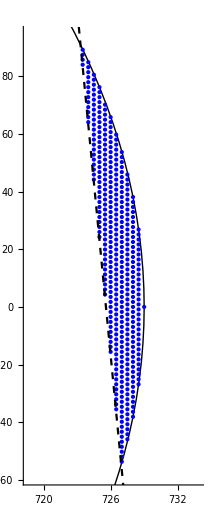

```mathematica
(*Define constants*)
alpha=0.05/2;
tol = 0.1;
k=12;
r1=3^(Ceiling[k/2]) * (1 - tol^2/2);
r2=3^(Ceiling[k/2]);
δ = 5;

(*Solve for y in terms of x using the line equation*)
lineFunction=Solve[x Cos[alpha]+y Sin[alpha]==r1,y][[1,1]];

(*Plot the circle and the line*)
(*Plot the circle,line,and data points*)Show[Graphics[{Circle[{0,0},r2]}],ListPlot[data,PlotStyle->{Blue,PointSize[Medium]}],Plot[Evaluate[y/. lineFunction],{x,-r2-1,r2+1},PlotStyle->{Dashed, Black}],Axes->True,PlotRange->{{xmin-δ,xmax+δ},{ymin-δ,ymax+δ}}]
```

```mathematica
ω = Exp[2π ⅈ/3];
zz[a_,b_]:=a + b ω
ff = zz[1,2]; 
err[x_]:=Sqrt[2(1 - Re[x * Exp[-ⅈ alpha]/ff^k])]
```